```mathematica
Clear["Global`*"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Sampler1`";
```

```mathematica
HessianH[f_,x_List?VectorQ]:=D[f,{x,2}];
GradientG[f_,x_List?VectorQ]:=D[f,{x,1}];
a=1;
b=100;
U[x_,y_]=(a-x)^2+b (y-x^2)^2;
dU[x_,y_]=GradientG[U[x,y],{x,y}];
ddU[x_,y_]=HessianH[U[x,y],{x,y}];
QShmc=hmc[U,dU,ddU,2,2000,4000,True,False];
QSrhmc=hmc[U,dU,ddU,2,2000,4000,False,False];
QSchmc=hmc[U,dU,ddU,2,2000,4000,True,True];
```

1001 293.931 5.66511 0.601126 0.432617 7.26902 301.2 300 0.00129526 0.001 True {1,5,7,11} {1,3,11}

2002 289.352 8.5699 0.47617 0.409795 11.8483 301.2 300 0.00107214 0.001 True {1,11} {1,11}

3003 289.096 10.3452 0.481482 0.407222 12.104 301.2 300 0.00107214 0.001 True {1,2,8,11} {1,11}

1001 350.589 1.1874 0.731956 0.311811 29.702 300 380.291 0.001 0.0236699 False {1,11} {1,5,8,11}

2002 373.064 0.817513 0.615169 0.40706 13.2038 300 386.268 0.001 0.0494286 False {1,11} {1,11}

3003 375. 3.46287 0.767607 0.377007 11.2681 300 386.268 0.001 0.0494286 False {1,11} {1,2,8,11}

1001 287.948 9.95353 0.593169 0.404534 12.8076 300.756 373.3 0.00105101 0.00605576 True {1,3,4,5,6,11} {1,11}

2002 400.78 0.543966 0.671347 0.308415 8.93565 300.756 409.716 0.00105101 0.0108926 False {1,3,7,11} {1,8,11}

3003 290.896 14.7594 0.513529 0.46815 9.86004 300.756 409.716 0.00105101 0.0108926 True {1,7,8,11} {1,11}

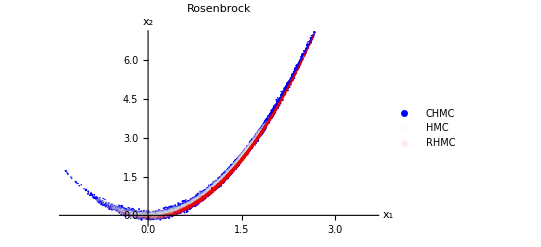

```mathematica
ListPlot[{QSchmc,QShmc,QSrhmc},PlotStyle->{Directive[Opacity[1],Blue],Directive[Opacity[.1],LightGray],Directive[Opacity[.07],Red]},PlotLegends->{Style["CHMC",Blue],Style["HMC",Gray],Style["RHMC",Red]},PlotLabel->Rosenbrock,AxesLabel->{"x_1","x_2"}]
```

10 chains trace

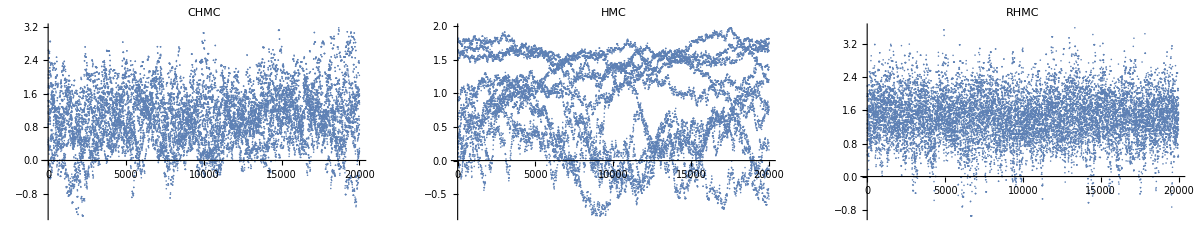

```mathematica
GraphicsRow[{ListPlot[QSchmc[[;;,1]],PlotLabel->"CHMC"],ListPlot[QShmc[[;;,1]],PlotLabel->"HMC"],ListPlot[QSrhmc[[;;,1]],PlotLabel->"RHMC"]}]
```